```mathematica
ClearAll["`*"];
```

```mathematica
pfX[k_]:=Piecewise[{{1/4, k==4},{1/6, k==6},{1/8,k==8},{1/12,k==12},{1/20,k==20}},0]
```

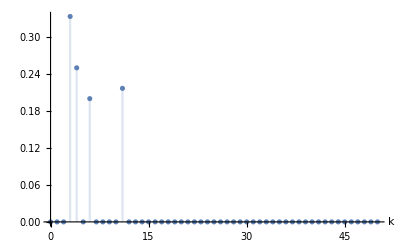

```mathematica
DiscretePlot[pfX[k],{k,0,50},AxesLabel->Automatic]
```

```mathematica
cdfX[x_]:=With[{n=Floor[x]},Sum[pfX[k],{k,1,n}]]
```

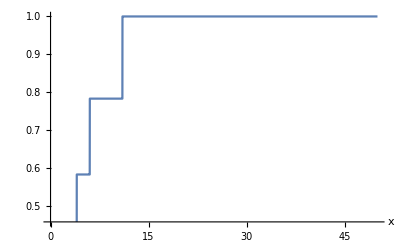

```mathematica
Plot[cdfX[x],{x,0,50},AxesLabel->Automatic]
```

```mathematica
ClearAll["`*"]
pfA[i_]= PDF[BinomialDistribution[4,0.25],i]
pfB[i_]=PDF[BinomialDistribution[6,(1/6)],i]
```

Piecewise[{{0.25^i 0.75^(4-i) Binomial[4,i], 0≤i≤4}, {0, True}}]

Piecewise[{{(5^(6-i) Binomial[6,i])/46656, 0≤i≤6}, {0, True}}]

```mathematica
pfL[l_]:=pfL[l]=Sum[pfA[i]pfB[l-i],{i,0,10}]
```

```mathematica
Table[pfL[l],{l,2,10}]
```

{0.303763,0.202195,0.0876805,0.0258859,0.00527012,0.000730747,0.0000660586,3.51643×10^-6,8.37245×10^-8}

```mathematica
pfC[j_]= PDF[BinomialDistribution[8,(1/8)],j]
pfD[j_]= PDF[BinomialDistribution[12,(1/12)],j]
```

Piecewise[{{(7^(8-j) Binomial[8,j])/16777216, 0≤j≤8}, {0, True}}]

Piecewise[{{(11^(12-j) Binomial[12,j])/8916100448256, 0≤j≤12}, {0, True}}]

```mathematica
pfM[m_]:=pfM[m]=Sum[pfC[j]pfD[m-j],{j,0,20}]
```

```mathematica
Table[pfM[m],{m,2,20}]
```

{21381945052649524343/74793671549043867648,7125280676171919415/37396835774521933824,13418449678728989741/149587343098087735296,296487671079965827/9349208943630483456,163335232499074405/18698417887260966912,17948130809220535/9349208943630483456,25570917463865785/74793671549043867648,931670740673585/18698417887260966912,223453142333333/37396835774521933824,11044351331849/18698417887260966912,3593560939561/74793671549043867648,29905090735/9349208943630483456,3227171269/18698417887260966912,69479467/9349208943630483456,37305533/149587343098087735296,235087/37396835774521933824,8375/74793671549043867648,47/37396835774521933824,1/149587343098087735296}

```mathematica
pfL[k_]= PDF[BinomialDistribution[9,(1/24)],k]
pfM[k_]= PDF[BinomialDistribution[19,(1/96)],k]
```

Piecewise[{{(23^(9-k) Binomial[9,k])/2641807540224, 0≤k≤9}, {0, True}}]

Piecewise[{{(95^(19-k) Binomial[19,k])/46041920195771638718627820723247251456, 0≤k≤19}, {0, True}}]

```mathematica
pfN[n_]:=pfN[n]=Sum[pfL[k]pfM[n-k],{k,0,30}]
```

```mathematica
Table[pfN[n],{n,4,30}]
```

{0.297589,0.202701,0.117401,0.0580665,0.0245083,0.00883714,0.0027319,0.000727467,0.000167629,0.0000335524,5.84969×10^-6,8.89827×10^-7,1.18171×10^-7,1.3695×10^-8,1.38289×10^-9,1.2134×10^-10,9.21369×10^-12,6.02019×10^-13,3.35894×10^-14,1.58401×10^-15,6.22741×10^-17,2.00313×10^-18,5.13604×10^-20,1.01328×10^-21,1.5039×10^-23,2.12645×10^-25,6.45727×10^-27}

```mathematica
pfN[o_]= PDF[BinomialDistribution[27,(1/2304)],o]
pfE[o_]= PDF[BinomialDistribution[20,(1/20)],o]
```

Piecewise[{{(2303^(27-o) Binomial[27,o])/6123882063714047228748024892632328925882220459612696688795268197398201019720672383634243584, 0≤o≤27}, {0, True}}]

Piecewise[{{(19^(20-o) Binomial[20,o])/104857600000000000000000000, 0≤o≤20}, {0, True}}]

```mathematica
pfS[s_]:=pfS[s]=Sum[pfN[o]pfE[s-o],{o,0,50}]
```

```mathematica
Table[pfS[s],{s,0,50}]
```

{1/12,17/144,217/1728,2465/20736,26281/248832,269297/2985984,2685817/35831808,26269505/429981696,253202761/5159780352,2413042577/61917364224,22791125017/743008370688,213710059745/8916100448256,1992110014441/106993205379072,18478745943857/1283918464548864,170706760005817/15407021574586368,1571545212141185/184884258895036416,14425381885981321/2218611106740436992,132080236787517137/26623333280885243904,1206736529597136217/319479999370622926848,11004743954450081825/3833759992447475122176,100195617094657583401/46005119909369701466112,910983925888773026417/552061438912436417593344,8272642309293795444217/6624737266949237011120128,75044076594002864649665/79496847203390844133441536,680119055828895427060681/953962166440690129601298432,6158850434323016005255697/11447545997288281555215581184,55731885363810801340977817/137370551967459378662586974208,504004819913526470418212705/1648446623609512543951043690496,4555386192335572300559213161/19781359483314150527412524285952,41153218235930823239395308977/237376313799769806328950291431424,371616904162662789429456905017/2848515765597237675947403497177088,3354455657778248147064305138945/34182189187166852111368841966125056,30269329082518497661172290200841/410186270246002225336426103593500672,273057787042780593651298963410257/4922235242952026704037113243122008064,2462590685785938260467677483513817/59066822915424320448445358917464096768,22203880991280747685056991854196385/708801874985091845381344307009569161216,200159447475185155892296082708343721/8505622499821102144576131684114829934592,1804031175705933816844929992539703537/102067469997853225734913580209377959215104,16257049768787543662118491918174212217/1224809639974238708818962962512535510581248,146479601418561007443179403146102953025/14697715679690864505827555550150426126974976,1319645640762833982861518435375206921801/176372588156290374069930666601805113523699712,11887444590831785172736896374859105052817/2116471057875484488839167999221661362284396544,107072071909216301170497911025589887528217/25397652694505813866070015990659936347412758528,964329211916788587461407948445172524176865/304771832334069766392840191887919236168953102336,8684407425121832302568085529725461008975081/3657261988008837196714082302655030834027437228032,78203222969062370846436081717280415411842097/43887143856106046360568987631860370008329246736384,704177455865288378604511231053533869355109817/526645726273272556326827851582324440099950960836608,6340384695937411735333293044265885869384235905/6319748715279270675921934218987893281199411530039296,57085763008635236241141173116665621185964103561/75836984583351248111063210627854719374392938360471552,513950273039305371155402843796171777565724775377/910043815000214977332758527534256632492715260325658624,4626979705046454300279683880134995493227905725017/10920525780002579727993102330411079589912583123907903488}

```mathematica
Table[pfS[s],{s,0,10}]//N
```

{0.0833333,0.118056,0.125579,0.118875,0.105617,0.090187,0.0749562,0.0610945,0.0490724,0.038972,0.0306741}

```mathematica
Table[pfS[s],{s,45,50}]//N
```

{1.78192×10^-6,1.3371×10^-6,1.00327×10^-6,7.52743×10^-7,5.64753×10^-7,4.23696×10^-7}